```mathematica
sol=NDSolve[{u'[t]==u[t]*Cos [t],u[0]==0.5},u,{t,0,30}]
```

{{u→InterpolatingFunction[{{0.,30.}},<>]}}

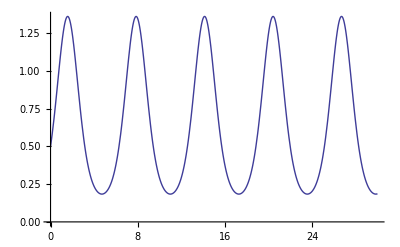

```mathematica
Plot[u[t]/.sol,{t,0,30}]
```

```mathematica
eqns={x'[t]==y[t],y'[t]==-x[t],x[0]== 0,y[0]==1};sol=DSolve[eqns,{x,y},t]
```

DSolve::dvnoarg: The function y appears with no arguments.

DSolve[{y==y[t],-x==-x[t],x[0]==0,y[0]==1},{x,y},t]

```mathematica
s=NDSolve[{a'[t]==1/2*188*b[t],b'[t]==-1/2*188*a[t],c'[t]==-1/2*188*d[t],d'[t]==1/2*188*c[t],a[0]==c[0]==1,b[0]==d[0]==0},{a,b, c, d},{t,2Pi}]
```

{{a→InterpolatingFunction[{{0.,6.28319}},<>],b→InterpolatingFunction[{{0.,6.28319}},<>],c→InterpolatingFunction[{{0.,6.28319}},<>],d→InterpolatingFunction[{{0.,6.28319}},<>]}}

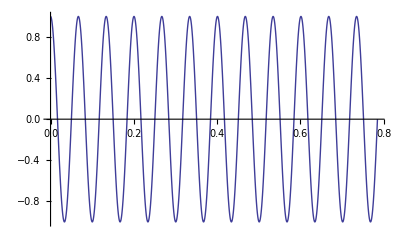

```mathematica
Plot[{a[t]/.s},{t,0,Pi/4}]
```

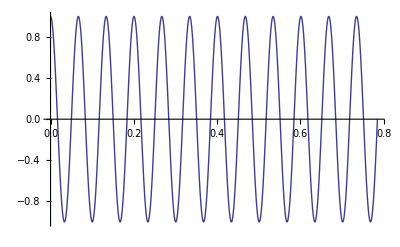

```mathematica
Plot[{Cos[188*t/2]},{t,0,Pi/4}]
```

```mathematica
w0=20
```

20

```mathematica
w=20
```

20

```mathematica
wl=3.1415
```

3.1415

```mathematica
s=NDSolve[{a'[t]==1/2*(w0*b[t]+wl*Cos[w*t]*d[t]),b'[t]==1/2*(-w0*a[t]-wl*Cos[w*t]*c[t]),c'[t]==1/2*(-w0*d[t]+wl*Cos[w*t]*b[t]),d'[t]==1/2*(w0*c[t]+wl*Cos[w*t]*a[t]),a[0]==1,b[0]==c[0]==d[0]==0},{a,b, c, d},{t,2Pi}]
```

{{a→InterpolatingFunction[{{0.,6.28319}},<>],b→InterpolatingFunction[{{0.,6.28319}},<>],c→InterpolatingFunction[{{0.,6.28319}},<>],d→InterpolatingFunction[{{0.,6.28319}},<>]}}

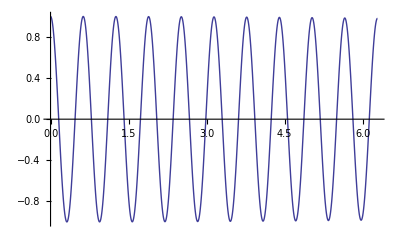

```mathematica
Plot[{a[t]/.s},{t,0,2*Pi}]
```

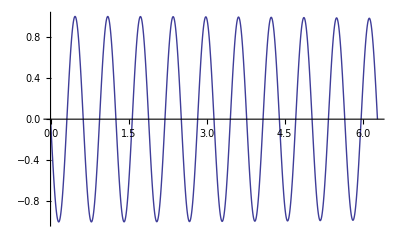

```mathematica
Plot[{b[t]/.s},{t,0,2*Pi}]
```

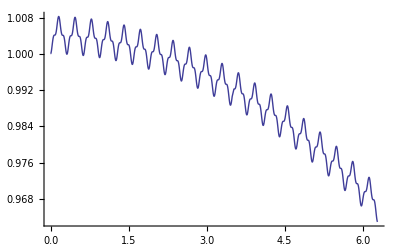

```mathematica
Plot[{a[t]^2+b[t]^2/.s},{t,0,2*Pi}]
```

```mathematica
w0=188
```

188

```mathematica
w=186
```

186

```mathematica
wc=1.57
```

1.57

```mathematica
s=NDSolve[{a'[t]==1/2*(-b[t]*(w-w0)+d[t]*wc),b'[t]==1/2*(a[t]*(w-w0)-c[t]*wc),c'[t]==1/2*(b[t]*wc+d[t]*(w-w0)),d'[t]==1/2*(-a[t]*wc-c[t]*(w-w0)),a[0]==1,b[0]==c[0]==d[0]==0},{a,b, c, d},{t,2Pi}]
```

{{a→InterpolatingFunction[{{0.,6.28319}},<>],b→InterpolatingFunction[{{0.,6.28319}},<>],c→InterpolatingFunction[{{0.,6.28319}},<>],d→InterpolatingFunction[{{0.,6.28319}},<>]}}

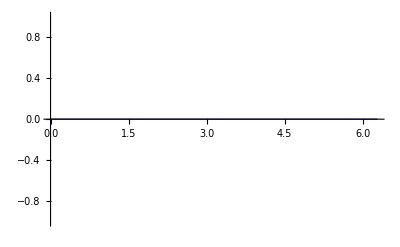

```mathematica
Plot[{b[t]/.s},{t,0,2*Pi}]
```

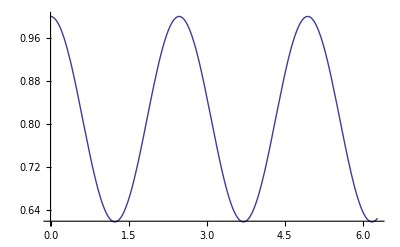

```mathematica
Plot[{(a[t]^2+b[t]^2)/.s},{t,0,2*Pi}]
```

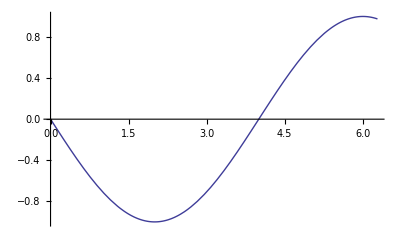

```mathematica
Plot[{d[t]/.s},{t,0,2*Pi}]
```